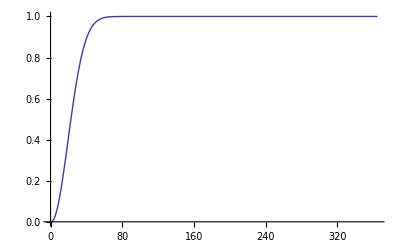

```mathematica
Plot[birthday[n], {n, 0, 365}, PlotRange->All]
```

```mathematica
birthday[days_, persons_] := N[1- FactorialPower[days, persons] / days^persons, 100];
```

```mathematica
birthday[30*365, 400]
```

0.9993751207324398545755756185365866158982418574884589984862400698949185357385545611490834109377426829

```mathematica
30*365
```

10950